```mathematica
mystyle={FontFamily->"Times",Italic,FontSize->15};
Off[NDSolve::"ndsz"]
xmin=10^-4 ;xend=25;
insl=0.50604324925;
s=NDSolve[{ψ''[x]+2 x^-1 ψ'[x]-2 x^-2 ψ[x]-(ψ[x]^2-1)ψ[x]==0,ψ[xmin]==xmin*insl,ψ'[xmin]==insl},ψ,{x,xmin,xend},PrecisionGoal->16];
Ψ[z_]=ψ[z]/.s[[1]];
xmax=18;
tab=Table[{z,Ψ[z]},{z,xmin,xmax,(xmax-xmin)/100.}];
fit=FindFit[tab,a Tanh[b z]+c Tanh[d z]+0*e Tanh[f z],{a,b,c,d,e,f},z];
 aa=fit[[1,2]];bb=fit[[2,2]];cc=fit[[3,2]];dd=fit[[4,2]];ee=fit[[5,2]];ff=fit[[6,2]];
(* Semianalytic approximation by means of Tanh functions *)
Φ[r_]=aa Tanh[bb r]+cc Tanh[dd r]+0*ee Tanh[ff r];(* Including more terms does not improve the performance *)

(* Eq A1 *) 
eq1=K22[t,r](2K[t,r]-3K22[t,r])-(2 Derivative[0,2][B][t,r])/(A[t,r]^2 B[t,r])-(Derivative[0,1][B][t,r])^2/(A[t,r]^2 B[t,r]^2)+(2 Derivative[0,1][A][t,r] Derivative[0,1][B][t,r])/(A[t,r]^3 B[t,r])-(6 Derivative[0,1][B][t,r])/(r A[t,r]^2 B[t,r])+(2 Derivative[0,1][A][t,r])/(r A[t,r]^3)-1/(r^2 A[t,r]^2)+1/(r^2 B[t,r]^2)==η^2(1/2(Derivative[1,0][ϕ][t,r])^2+(Derivative[0,1][ϕ][t,r])^2/(2 A[t,r]^2)+ϕ[t,r]^2/(B[t,r]^2 r^2)+1/4(ϕ[t,r]^2-1)^2+ρ[t,r]/(1-v[t,r]^2));
(* Eq. A2 *) eq2=D[K22[t,r], r]+((Derivative[0,1][B][t,r])/B[t,r]+1/r)(3K22[t,r]-K[t,r])==η^2/2(Derivative[1,0][ϕ][t,r]Derivative[0,1][ϕ][t,r]-v[t,r]/(1-v[t,r]^2)A[t,r]ρ[t,r]);
(* Eq. A3 *) eq3=D[K[t,r], t]-(K[t,r]-2K22[t,r])^2-2 K22[t,r]^2==η^2((Derivative[1,0][ϕ][t,r])^2-1/4(ϕ[t,r]^2-1)^2+1/2(1+v[t,r]^2)/(1-v[t,r]^2)ρ[t,r]);
(* Eq. A4c  eq4a=K11[t,r]==K[t,r]-2K22[t,r];*)
(* Eq. A4a *) eq4b=Derivative[1,0][A][t,r]==-A[t,r](K[t,r]-2K22[t,r]);
(* Eq. A4b *) eq4c=Derivative[1,0][B][t,r]==-B[t,r]K22[t,r];
(* Eq. A5 *) eq5=(Derivative[1,0][v][t,r])/v[t,r]==(v[t,r]^2-1)(Derivative[1,0][A][t,r])/A[t,r]-(Derivative[0,1][v][t,r])/A[t,r];
(* Eq. A6 for vdot, ρ given by A1 *) eq6=(Derivative[1,0][ρ][t,r])/ρ[t,r]==(Derivative[1,0][v][t,r])/v[t,r]-2(Derivative[1,0][B][t,r])/B[t,r]-v[t,r]/A[t,r](Derivative[0,1][ρ][t,r])/ρ[t,r]-2 v[t,r]/A[t,r](Derivative[0,1][B][t,r])/B[t,r]-2 v[t,r]/(r A[t,r]);
(* Eq. A7 *) eq7=Derivative[2,0][ϕ][t,r]-K[t,r] Derivative[1,0][ϕ][t,r]-(Derivative[0,2][ϕ][t,r])/A[t,r]^2-(-(Derivative[0,1][A][t,r])/A[t,r]+(2 Derivative[0,1][B][t,r])/B[t,r]+2/r)(Derivative[0,1][ϕ][t,r])/A[t,r]^2+(2ϕ[t,r])/(B[t,r]^2 r^2)+ϕ[t,r](ϕ[t,r]^2-1)==0;
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
(* Solution with η=0.1 *)
```

```mathematica
η=0.1  √(8π);
fraction=18;
V0=1/4;ρ0=1/4 fraction;
t0=√(16/(3 fraction η^2));
icond4a=A[t0,r]==1; (* normalized A *)
icond4b=B[t0,r]==1; (* normalized A *)
icond5=ϕ[t0,r]==Φ[r];
icond6=Derivative[1,0][ϕ][t0,r]==0;
icond8a=K22[t0,r]==-η/(√3)√(ρ0+1/4(Φ[r]^2-1)^2+Φ[r]^2/r^2+1/2 Φ'[r]^2);
icond8b=K[t0,r]==-(3η)/(√3)√(ρ0+1/4(Φ[r]^2-1)^2+Φ[r]^2/r^2+1/2 Φ'[r]^2);
icond9=ρ[t0,r]==ρ0;
icond10=v[t0,r]==10^-12;
(* Boundary conditions *)
bc1=ϕ[t,rmin]==Φ[rmin];
bc2=Derivative[0,1][ϕ][t,rmin]==Φ'[rmin];
bc4=K[t,rmin]==3K22[t,rmin];
```

```mathematica
Ztmax=0*620(* for η=7.5×10^-4 *)+0*270(* for η=2×10^-3 *)+0*130(* for η=4×10^-3 *)+0*70(* for η=7.5×10^-3 *)+0*50(* for η=0.01 *)+1*26(* for η=0.3 *);
tmax=t0+Ztmax;
Zrmin=10^-4;rmin=Zrmin ;
Zrmax=50;rmax=Zrmax;
Timing[solution=NDSolve[{eq2,eq3,eq4b,eq4c,eq5,eq6,eq7,icond4a,icond4b,icond5,icond6,icond8a,icond8b,icond9,icond10},{K,K22,A,B,ρ,ϕ,v},{t,t0,tmax},{r,rmin,rmax},AccuracyGoal->5,PrecisionGoal->5,MaxStepSize->{Automatic,Automatic}]]
```

NDSolve::ndode: The equations {K[1.08578,r]==-0.868322 √(9/2+1/2 Plus[«2»]^2+1/4 Plus[«2»]^2+Plus[«3»]^2/r^2)} are not differential equations or initial conditions in the dependent variables {A,B,K22,v,ρ,ϕ}.

{0.060314,NDSolve[{(-K[t,r]+3 K22[t,r]) (1/r+(B^(0,1)[t,r])/B[t,r])+K22^(0,1)[t,r]==0.125664 (-(A[t,r] v[t,r] ρ[t,r])/(1-v[t,r]^2)+ϕ^(0,1)[t,r] ϕ^(1,0)[t,r]),-(K[t,r]-2 K22[t,r])^2-2 K22[t,r]^2+K^(1,0)[t,r]==0.251327 (((1+v[t,r]^2) ρ[t,r])/(2 (1-v[t,r]^2))-1/4 (-1+ϕ[t,r]^2)^2+(ϕ^(1,0)[t,r])^2),A^(1,0)[t,r]==-A[t,r] (K[t,r]-2 K22[t,r]),B^(1,0)[t,r]==-B[t,r] K22[t,r],(v^(1,0)[t,r])/v[t,r]==-(v^(0,1)[t,r])/A[t,r]+((-1+v[t,r]^2) A^(1,0)[t,r])/A[t,r],(ρ^(1,0)[t,r])/ρ[t,r]==-(2 v[t,r])/(r A[t,r])-(2 v[t,r] B^(0,1)[t,r])/(A[t,r] B[t,r])-(v[t,r] ρ^(0,1)[t,r])/(A[t,r] ρ[t,r])-(2 B^(1,0)[t,r])/B[t,r]+(v^(1,0)[t,r])/v[t,r],(2 ϕ[t,r])/(r^2 B[t,r]^2)+ϕ[t,r] (-1+ϕ[t,r]^2)-((2/r-(A^(0,1)[t,r])/A[t,r]+(2 B^(0,1)[t,r])/B[t,r]) ϕ^(0,1)[t,r])/A[t,r]^2-(ϕ^(0,2)[t,r])/A[t,r]^2-K[t,r] ϕ^(1,0)[t,r]+ϕ^(2,0)[t,r]==0,A[1.08578,r]==1,B[1.08578,r]==1,ϕ[1.08578,r]==0.+43.3973 Tanh[1.64883 r]-42.7482 Tanh[1.66631 r],ϕ^(1,0)[1.08578,r]==0,K22[1.08578,r]==-0.289441 √(9/2+1/2 (71.5546 Sech[1.64883 r]^2-71.2319 Sech[1.66631 r]^2)^2+1/4 (-1+(0.+43.3973 Tanh[1.64883 r]-42.7482 Tanh[1.66631 r])^2)^2+(0.+43.3973 Tanh[1.64883 r]-42.7482 Tanh[1.66631 r])^2/r^2),K[1.08578,r]==-0.868322 √(9/2+1/2 (71.5546 Sech[1.64883 r]^2-71.2319 Sech[1.66631 r]^2)^2+1/4 (-1+(0.+43.3973 Tanh[1.64883 r]-42.7482 Tanh[1.66631 r])^2)^2+(0.+43.3973 Tanh[1.64883 r]-42.7482 Tanh[1.66631 r])^2/r^2),ρ[1.08578,r]==9/2,v[1.08578,r]==1/1000000000000},{K,K22,A,B,ρ,ϕ,v},{t,1.08578,27.0858},{r,1/10000,50},AccuracyGoal→5,PrecisionGoal→5,MaxStepSize→{Automatic,Automatic}]}

```mathematica
(* Define normalized scale factors *)
```

```mathematica
ol=0.73;
rat=(1-ol)/(4 ol); (* set value for Omega_Lambda and dtermine ratio of energy densities at present *)
sol:=Sqrt[ol];
Clear[ff,amon0,bmon0,amon0n,bmon0n,alcdm,alcdmn];
ff[Zt1_]:=Part[ρ[t0+Zt,0]/.solution  /. Zt->Zt1,1];
tp1=FindRoot[ff[tt] == rat,{tt,1}][[1,2]];  (* determine present time in monopole case using the density ratio  *)
tp=t0+tp1  (* this is the actual present time *)
amon0[t_]:=A[t,0] /. solution[[1]];
bmon0[t_]:=B[t,0] /. solution[[1]];  (* scale factors in the center  *)
amon20[t_]:=A[t,20] /. solution[[1]];
bmon20[t_]:=B[t,20] /. solution[[1]];  (* scale factors far away *)
h0r:=(2/3)ArcTanh[sol]/(tp sol);  (* the rescaled hubble parameter is obtained by demanding the same age of the universe for both lcdm and mopole core expansion. see also http://www.lsw.uni-heidelberg.de/users/mcamenzi/Day_1_LCDM_2010.pdf *)
alcdm[t_]:=((1-ol)/ol)^(1/3) Sinh[3 sol h0r t/2]^(2/3);  (* the lcdm scale factor. see also http://www.lsw.uni-heidelberg.de/users/mcamenzi/Day_1_LCDM_2010.pdf *)
amatn[t_]:=(t/tp)^(2/3);  (* the matter scale factor normalized to 1 at present *)
amon0n[t_]:=amon0[t]/amon0[tp];  (* the monopole core scale factor normalized to 1 at present *)
bmon0n[t_]:=bmon0[t]/bmon0[tp]; (* the monopole core scale factor normalized to 1 at present *)
amon20n[t_]:=amon20[t]/amon20[tp];   (* the monopole scale factor away from core normalized to 1 at present *)
bmon20n[t_]:=bmon20[t]/bmon20[tp]; (* the monopole scale factor away from core normalized to 1 at present *)
alcdmn[t_]:=alcdm[t]/alcdm[tp];  (* the lcdm scale factor away from core normalized to 1 at present *)
```

5.6377

```mathematica
(* Define Subscript[H, A](r,t) and Subscript[H, B](r,t) *)
```

```mathematica
amon[t_,r_]:=A[t,r] /. solution[[1]];
amonn[t_,r_]:=amon[t,r]/amon[tp,r];  (* the monopole scale factor normalized to 1 at present *)
hhmon[t_,r_]:=D[amonn[t1,r],t1]/amonn[t1,r] /. t1->t;

bmon[t_,r_]:=B[t,r] /. solution[[1]];  (* scale factors at any r  *)
bmonn[t_,r_]:=bmon[t,r]/bmon[tp,r]; (* the monopole scale factor normalized to 1 at present *)
hhmonb[t_,r_]:=D[bmonn[t1,r],t1]/bmonn[t1,r] /. t1->t;

ttmon[aa_,r_]:=FindRoot[amonn[t,r]==aa,{t,tp}][[1,2]];
ttmonb[aa_,r_]:=FindRoot[bmonn[t,r]==aa,{t,tp}][[1,2]];

hhamon[a_,r_]:=hhmon[ttmon[a,r],r];
hhamonb[a_,r_]:=hhmonb[ttmonb[a,r],r];
```

```mathematica
(* Define Hubble expansion rate *)
```

```mathematica
hhlcdm[t_]:=D[alcdmn[t1],t1]/alcdmn[t1] /. t1->t;  (* the hubble expansion rates in each case *)
hhamon0[t_]:=D[amon0n[t1],t1]/amon0n[t1] /. t1->t;
hhamat[t_]:=D[amatn[t1],t1]/amatn[t1] /. t1->t;
hhmon20[t_]:=D[amon20n[t1],t1]/amon20n[t1] /. t1->t;
```

```mathematica
ttmon0[aa_]:=FindRoot[amon0n[t]==aa,{t,tp}][[1,2]];
ttlcdm[aa_]:=FindRoot[alcdm[t]==aa,{t,tp}][[1,2]];
ttmat[aa_]:=FindRoot[amatn[t]==aa,{t,tp}][[1,2]];
```

```mathematica
(* Evaluate luminosity distances in the homogeneous core approximation *)
```

```mathematica
dlmon0[a_]:=NIntegrate[1/amon0n[t],{t,ttmon0[a],tp}]/a;
dlzmon0[z_]:=dlmon0[1/(1+z)];
dllcdm[a_]:=NIntegrate[1/alcdmn[t],{t,ttlcdm[a],tp}]/a;
dlzlcdm[z_]:=dllcdm[1/(1+z)];
dlmat[a_]:=NIntegrate[1/amatn[t],{t,ttmat[a],tp}]/a;
dlzmat[z_]:=dlmat[1/(1+z)];
```

```mathematica
(* Reads the data for the Union2 set with directional info. note that equatorial and not galactic coordinates are used *)
SetDirectory[NotebookDirectory[]];
Off[NIntegrate::"inum",NIntegrate::"inumr",General::"obspkg"];
datanw=ReadList["union2.txt",{Word,Number,Number,Number}];
ndat=Length[datanw];
 zdat=datanw[[#,2]]&;  (* redshifts are in the cmb frame *)
 mgndat=datanw[[#,3]]&;
errdat=datanw[[#,4]]&;
```

```mathematica
(* Define χ^2 and compute best fit parameters *)
```

```mathematica
sint=0; Clear[mb];
chi2mon[mb_]:=Sum[(mgndat[i]-5 Log[10,dlzmon0[zdat[i]]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
chi2mat[mb_]:=Sum[(mgndat[i]-5 Log[10,dlzmat[zdat[i]]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
chi2lcdm[mb_]:=Sum[(mgndat[i]-5 Log[10,dlzlcdm[zdat[i]]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
Off[FindRoot::"lstol"]
chminlcdm=FindMinimum[chi2lcdm[mb],{mb,0}]
chminmon=FindMinimum[chi2mon[mb],{mb,0}]
chminmat=FindMinimum[chi2mat[mb],{mb,0}]
```

{542.683,{mb→39.3869}}

{543.686,{mb→39.3992}}

{1107.27,{mb→38.7502}}

```mathematica
(* Check Hamiltonian constraint up to tp *)
```

```mathematica
(* Lefthand side and righthand side or the Hamiltonian constraint *)
```

```mathematica
lhsHam[t_,r_]=K22[t,r](2K[t,r]-3K22[t,r])-(2 Derivative[0,2][B][t,r])/(A[t,r]^2 B[t,r])-(Derivative[0,1][B][t,r])^2/(A[t,r]^2 B[t,r]^2)+(2 Derivative[0,1][A][t,r] Derivative[0,1][B][t,r])/(A[t,r]^3 B[t,r])-(6 Derivative[0,1][B][t,r])/(r A[t,r]^2 B[t,r])+(2 Derivative[0,1][A][t,r])/(r A[t,r]^3)-1/(r^2 A[t,r]^2)+1/(r^2 B[t,r]^2);
rhsHam[t_,r_]=η^2(1/2(Derivative[1,0][ϕ][t,r])^2+(Derivative[0,1][ϕ][t,r])^2/(2 A[t,r]^2)+ϕ[t,r]^2/(B[t,r]^2 r^2)+1/4(ϕ[t,r]^2-1)^2+ρ[t,r]/(1-v[t,r]^2));
```

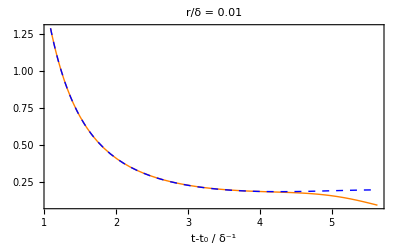
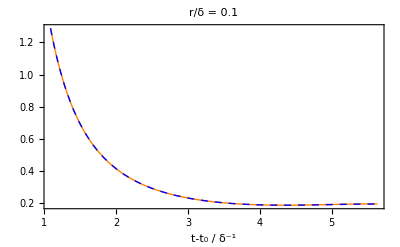
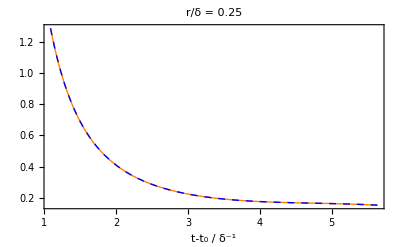
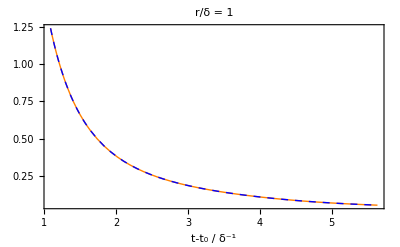
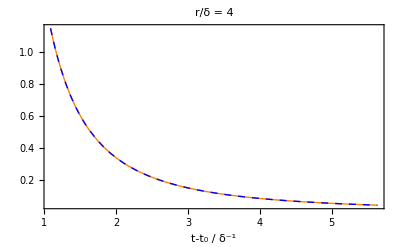
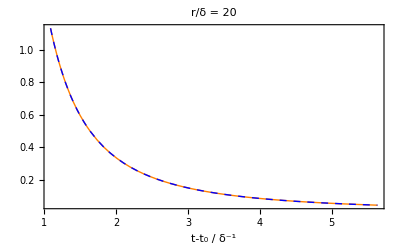

```mathematica
Plot[{lhsHam[t,#]/.solution,rhsHam[t,#]/.solution},{t,t0,tp},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"t-t_0 / δ^-1",""},PlotLabel->"r/δ = "<>ToString[#],PlotStyle->{Orange,{Blue,Dashed}}]&/@{0.01,0.1,0.25,1,4,20}
```

```mathematica
(* % difference between lefthand side and righthand side in the Hamiltonian constraint *)
```

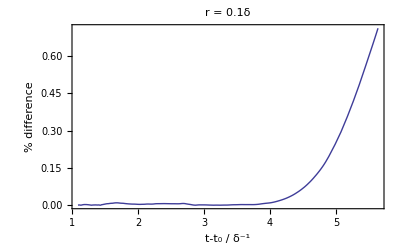
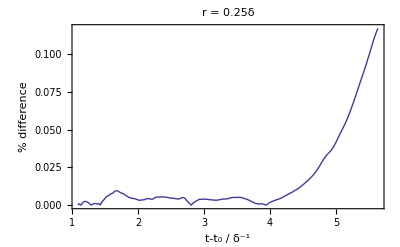
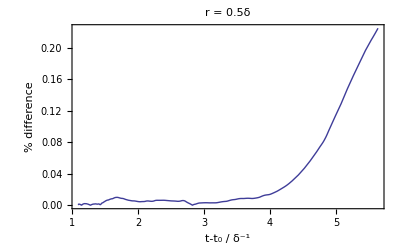
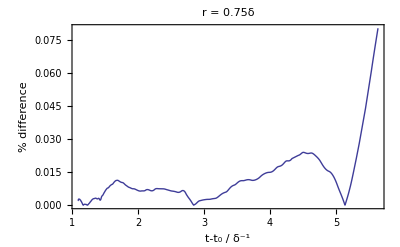
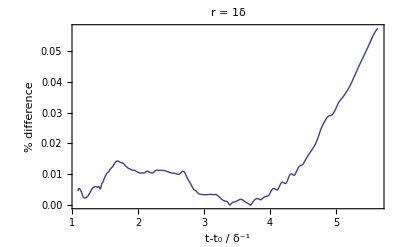
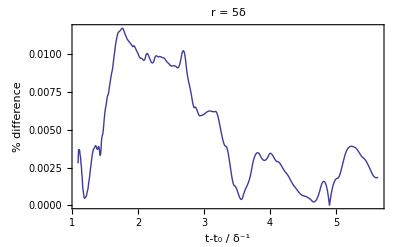

```mathematica
Plot[Abs[((lhsHam[t,#]-rhsHam[t,#])/lhsHam[t,#])/.solution]*100,{t,t0,tp},Frame->True,Axes->False,PlotRange->All,FrameLabel->{"t-t_0 / δ^-1","% difference"},PlotLabel->"r = "<>ToString[#]<>"δ"]&/@{0.1,0.25,0.5,0.75,1,5}
```

# Plots

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Figure 1a *)
```

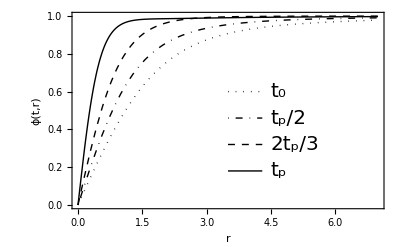

fig1a.eps

```mathematica
curves=ϕ[#,r]&/@{t0,tp/2,(2tp)/3,tp}/.solution;
plot=Plot[curves,{r,rmin,7},Frame->True,Axes->False,FrameLabel->{"r","ϕ(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Dotted,Black},{DotDashed,Black},{Dashed,Black},{Black,Thin}}];
(* build legend *)
styles={Dotted,DotDashed,Dashed,Thin};
times={"t_0","t_p/2","2t_p/3","t_p"};
hp=3.5;vp=0.6;sp=0.14;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd1=Graphics[Table[{Directive[styles[[i1]]],Text[Style[times[[i1]],20],{hp+1,vp-sp(i1-1)},{-1,0}],Line[{{hp,vp-sp(i1-1)},{hp+0.8,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];
Show[plot,lgd1]
Export["fig1a.eps",Show[plot,lgd1]]
```

```mathematica
(* Figure 2 *)
```

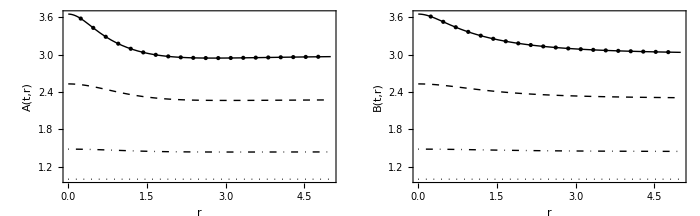

```mathematica
Clear[curves,curvesA1,curvesA2,curvesB1,curvesB2]
curvesA1=A[#,r]&/@{t0,tp/3,(2tp)/3}/.solution;
curvesA2=A[#,r]&/@{tp}/.solution;
curvesB1=B[#,r]&/@{t0,tp/3,(2tp)/3}/.solution;
curvesB2=B[#,r]&/@{tp}/.solution;
p1a=Plot[curvesA1,{r,rmin,5},Frame->True,Axes->False,FrameLabel->{"r","A(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,
PlotStyle->{{Thick,Dotted,Black},{DotDashed,Black},{Dashed,Black}}];
p1b=Plot[curvesA2,{r,rmin,5},Frame->True,Axes->False,FrameLabel->{"r","A(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{Black,Thin},Mesh->20];
p1=Show[p1a,p1b];
p2a=Plot[curvesB1,{r,rmin,5},Frame->True,Axes->False,FrameLabel->{"r","B(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Thick,Dotted,Black},{DotDashed,Black},{Dashed,Black}}];
p2b=Plot[curvesB2,{r,rmin,5},Frame->True,Axes->False,FrameLabel->{"r","B(t,r)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{Black,Thin},Mesh->20];
p2=Show[p2a,p2b];
Show[GraphicsGrid[{{p1,p2}},Spacings->0],ImageSize->700]
```

```mathematica
(* Import plots with η=0.6 *)
```

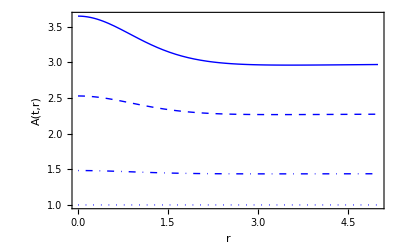
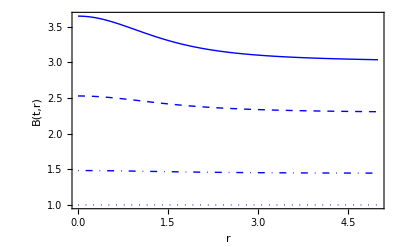
```mathematica
pp1=-Graphics-;pp2=-Graphics-;
```

fig2a.eps

fig2b.eps

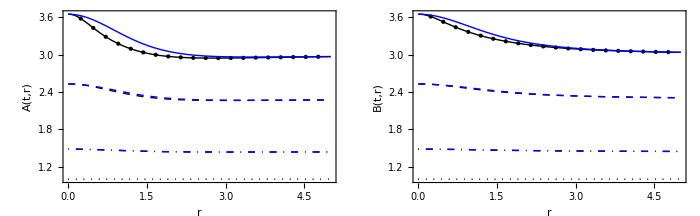

```mathematica
Export["fig2a.eps",Show[p1,pp1]]
Export["fig2b.eps",Show[p2,pp2]]
Show[GraphicsGrid[{{Show[p1,pp1],Show[p2,pp2]}},Spacings->0],ImageSize->700]
```

```mathematica
(* Figure 3 *)
```

```mathematica
(* Define Subscript[H, A](r,t) and Subscript[H, B](r,t) *)
```

```mathematica
amon[t_,r_]:=A[t,r] /. solution[[1]];
amonn[t_,r_]:=amon[t,r]/amon[tp,r];  (* the monopole scale factor normalized to 1 at present *)
hhmon[t_,r_]:=D[amonn[t1,r],t1]/amonn[t1,r] /. t1->t;

bmon[t_,r_]:=B[t,r] /. solution[[1]];  (* scale factors at any r  *)
bmonn[t_,r_]:=bmon[t,r]/bmon[tp,r]; (* the monopole scale factor normalized to 1 at present *)
hhmonb[t_,r_]:=D[bmonn[t1,r],t1]/bmonn[t1,r] /. t1->t;

ttmon[aa_,r_]:=FindRoot[amonn[t,r]==aa,{t,tp}][[1,2]];
ttmonb[aa_,r_]:=FindRoot[bmonn[t,r]==aa,{t,tp}][[1,2]];

hhamon[a_,r_]:=hhmon[ttmon[a,r],r];
hhamonb[a_,r_]:=hhmonb[ttmonb[a,r],r];
```

```mathematica
(* Define H(a) for LCDM *)
```

```mathematica
hhalcdm[a_]:=hhlcdm[ttlcdm[a]];
```

```mathematica
(* Define H for EdS *)
```

```mathematica
hhmat[t_]:=D[amatn[t1],t1]/amatn[t1] /. t1->t;
hhamat[a_]:=hhmat[ttmat[a]];
```

fig3a.eps

fig3b.eps

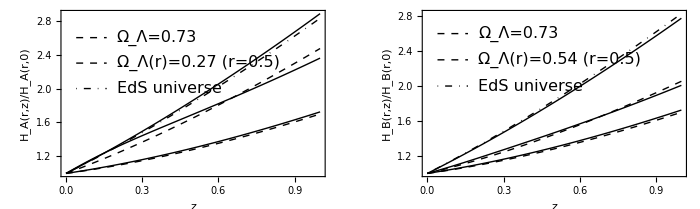

```mathematica
Clear[curvesA,curvesB,curvelcdm,curvemat];
curvesA[z_]:=hhamon[1/(1+z),#]/hhamon[1,#]&/@{0,0.5,5};curvesB[z_]:=hhamonb[1/(1+z),#]/hhamonb[1,#]&/@{0,0.5,5};
curvelcdm[z_]:=hhalcdm[1/(1+z)]/hhalcdm[1];curvemat[z_]:=hhamat[1/(1+z)]/hhamat[1];
ol=0.73;
p1=Plot[{curvesA[z],curvelcdm[z],curvemat[z]},{z,0,1},Frame->True,Axes->False,FrameLabel->{"z","H_A(r,z)/H_A(r,0)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Black},{Thick,Black,Dashed},{Black,DotDashed}}];
p2=Plot[{curvesB[z],curvelcdm[z],curvemat[z]},{z,0,1},Frame->True,Axes->False,FrameLabel->{"z","H_B(r,z)/H_B(r,0)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Black},{Thick,Black,Dashed},{Black,DotDashed}}];
ol=0.27;(* Best fit ol from Figure 4 *)
p3=Plot[curvelcdm[z],{z,0,1},Frame->True,Axes->False,FrameLabel->{"z","H_A(r,z)/H_A(r,0)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,
PlotStyle->{Black,Dashed}];
ol=0.54;(* Best fit ol from Figure 4 *)
p4=Plot[curvelcdm[z],{z,0,1},Frame->True,Axes->False,FrameLabel->{"z","H_B(r,z)/H_B(r,0)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{Black,Dashed}];
(* build legends *)
styles={{Thick,Dashed},Dashed,DotDashed};
text={"Ω_Λ=0.73","Ω_Λ(r)=0.27 (r=0.5)","EdS universe"};
hp=0.08;vp=2.6;sp=0.3;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd1=Graphics[Table[{Directive[styles[[i1]]],Text[Style[text[[i1]],16],{hp+0.12,vp-sp(i1-1)},{-1,0}],Line[{{hp-0.04,vp-sp(i1-1)},{hp+0.08,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];
text={"Ω_Λ=0.73","Ω_Λ(r)=0.54 (r=0.5)","EdS universe"};
hp=0.08;vp=2.6;sp=0.3;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd2=Graphics[Table[{Directive[styles[[i1]]],Text[Style[text[[i1]],16],{hp+0.12,vp-sp(i1-1)},{-1,0}],Line[{{hp-0.04,vp-sp(i1-1)},{hp+0.08,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];

plot1=Show[p1,p3,lgd1];
plot2=Show[p2,p4,lgd2];
Export["fig3a.eps",plot1]
Export["fig3b.eps",plot2]
Show[GraphicsGrid[{{plot1,plot2}}],ImageSize->700]
```

```mathematica
(* Figure 4 *)
```

```mathematica
(* Scale factor A *)
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

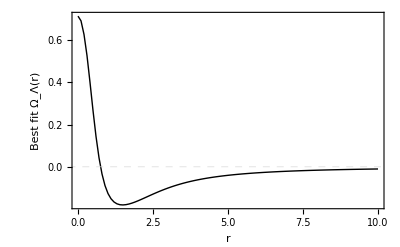

```mathematica
rmin=0;rmax=10;nr=100; dr=(rmax-rmin)/nr; (* Find best fit values of \Omega_L(r) *)
Do[amin=0.5; amax=1; nn=100; da=(amax-amin)/nn; r=rmin+(j-1) dr;
tab=Table[{amin+da (i-1),hhamon[amin+da (i-1),r]/hhamon[1,r]},{i,1,nn+1}];
model=Sqrt[olx+(1-olx)/a^3];r=.;
fit=FindFit[tab,model,olx,a];
olxx[j]=olx /. fit,{j,1,nr+1}]
olxtab=Table[{rmin+(j-1) dr //N,olxx[j]},{j,1,nr+1}];
bestfitolA=Interpolation[olxtab];
pA=ListPlot[olxtab,PlotStyle->{Black},PlotRange->All,Joined->True,Frame->True,Axes->False,FrameLabel->{"r","Best fit Ω_Λ(r)"},BaseStyle->mystyle,GridLines->{{},{{0,Dashed}}}]
```

```mathematica
(* Scale factor B *)
```

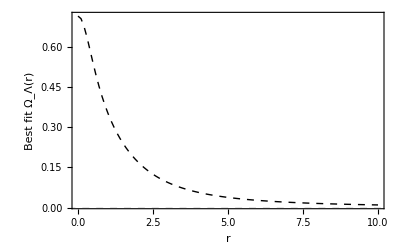

```mathematica
rmin=0;rmax=10;nr=100; dr=(rmax-rmin)/nr; (* Find best fit values of \Omega_L(r) *)
Do[
amin=0.5; amax=1; nn=100; da=(amax-amin)/nn; r=rmin+(j-1) dr;
tab=Table[{amin+da (i-1),hhamonb[amin+da (i-1),r]/hhamonb[1,r]},{i,1,nn+1}];
model=Sqrt[olx+(1-olx)/a^3];
fit=FindFit[tab,model,olx,a];
olxx[j]=olx /. fit,{j,1,nr+1}];r=.;
olxtab=Table[{rmin+(j-1) dr //N,olxx[j]},{j,1,nr+1}];
bestfitolB=Interpolation[olxtab];
pB=ListPlot[olxtab,PlotStyle-> {Black,Dashed},PlotRange->All,Joined->True,Frame->True,Axes->False,FrameLabel->{"r","Best fit Ω_Λ(r)"},BaseStyle->mystyle,GridLines->{{},{{0,Dashed}}}]
```

```mathematica
(* Legends *)
styles={Thin,Dashed};
text={"for H_A=_Ȧ/A","for H_B=_Ḃ/B"};
hp=4.5;vp=0.5;sp=0.15;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd=Graphics[Table[{Directive[styles[[i1]]],Text[Style[text[[i1]],16],{hp+0.2,vp-sp(i1-1)},{-1,0}],Line[{{hp-1.2,vp-sp(i1-1)},{hp,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];
```

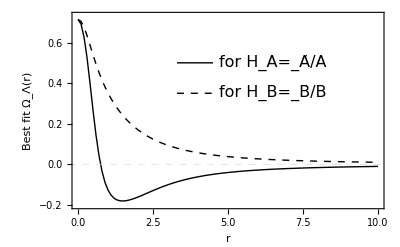

fig4.eps

```mathematica
plot=Show[pA,pB,lgd,PlotRange->{{0,10},{-0.2,0.73}},PlotRangePadding->{0.25,0.05},ImageSize->400]
Export["fig4.eps",plot]
```

```mathematica
(* Figure 5 *)
```

fig5a.eps

fig5b.eps

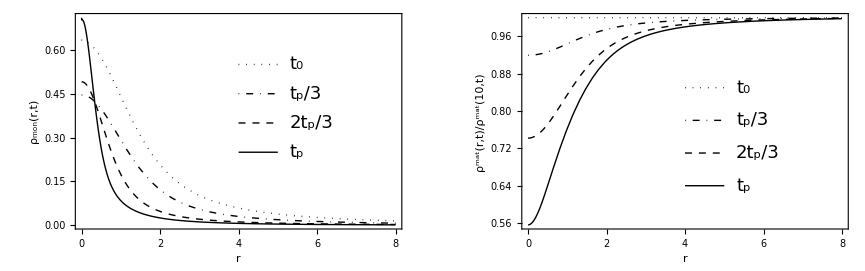

```mathematica
Clear[curves];
ρmon[t_,r_]=(1/2(Derivative[1,0][ϕ][t,r])^2+(Derivative[0,1][ϕ][t,r])^2/(2 A[t,r]^2)+ϕ[t,r]^2/(B[t,r]^2 r^2)+1/4(ϕ[t,r]^2-1)^2)/.solution;
curves=ρmon[#,r]&/@{t0,tp/3,(2tp)/3,tp};
plotA=Plot[curves,{r,rmin,8},Frame->True,Axes->False,FrameLabel->{"r","ρ_mon(r,t)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Dotted,Black},{DotDashed,Black},{Dashed,Black},{Black,Thin}}];
(* build legends *)
styles={Dotted,DotDashed,Dashed,Thin};
times={"t_0","t_p/3","2t_p/3","t_p"};
hp=4;vp=0.55;sp=0.1;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd1=Graphics[Table[{Directive[styles[[i1]]],Text[Style[times[[i1]],18],{hp+1.3,vp-sp(i1-1)},{-1,0}],Line[{{hp,vp-sp(i1-1)},{hp+1,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];
hp=4;vp=0.85;sp=0.07;(* horizontal position (hp), vertical position (vp), separation (sp) *)
lgd2=Graphics[Table[{Directive[styles[[i1]]],Text[Style[times[[i1]],18],{hp+1.3,vp-sp(i1-1)},{-1,0}],Line[{{hp,vp-sp(i1-1)},{hp+1,vp-sp(i1-1)}}]},{i1,1,Length[styles]}]];
curves=ρ[#,r]/ρ[#,10]&/@{t0,tp/3,(2tp)/3,tp}/.solution;
plotB=Plot[curves,{r,rmin,8},Frame->True,Axes->False,FrameLabel->{"r","ρ^mat(r,t)/ρ^mat(10,t)"},BaseStyle->mystyle,ImageSize->400,PlotRange->All,PlotStyle->{{Dotted,Black},{DotDashed,Black},{Dashed,Black},{Black,Thin}},PlotRangePadding->{0.1,0.01}];
Export["fig5a.eps",Show[plotA,lgd1]]
Export["fig5b.eps",Show[plotB,lgd2]]
GraphicsGrid[{{Show[plotA,lgd1],Show[plotB,lgd2]}}]
```

```mathematica
(* Figure 6 *)
```

```mathematica
(* Figure 6a *)
```

```mathematica
(* Reads the data for the Union2 set with directional info. note that equatorial and not galactic coordinates are used *)
Off[NIntegrate::"inum",NIntegrate::"inumr",General::"obspkg",FindRoot::"lstol",FindRoot::"njnum"]
datanw=ReadList["union2.txt",{Word,Number,Number,Number}];
ndat=Length[datanw];
 zdat=datanw[[#,2]]&;  (* redshifts are in the cmb frame *)
 mgndat=datanw[[#,3]]&;
errdat=datanw[[#,4]]&;
```

```mathematica
(* Define χ^2 and find best fit parameter *)
sint=0; Clear[mb];ol=0.73;
chi2mon[mb_]:=Sum[(mgndat[i]-5 Log[10,dlzmon0[zdat[i]]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
chi2mat[mb_]:=Sum[(mgndat[i]-5 Log[10,dlzmat[zdat[i]]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
chi2lcdm[mb_]:=Sum[(mgndat[i]-5 Log[10,dlzlcdm[zdat[i]]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
```

```mathematica
chminlcdm=FindMinimum[chi2lcdm[mb],{mb,0}]
chminmon=FindMinimum[chi2mon[mb],{mb,0}]
chminmat=FindMinimum[chi2mat[mb],{mb,0}]
```

{542.683,{mb→39.3869}}

{543.686,{mb→39.3992}}

{1107.27,{mb→38.7502}}

```mathematica
dlmon[a_,r_]:=NIntegrate[1/bmonn[t,r],{t,ttmonb[a,r],tp}]/a;
dlzmon[z_,r_]:=dlmon[1/(1+z),r];
```

```mathematica
Needs["ErrorBarPlots`"]
Off[InterpolatingFunction::dmval];
chi2monr[mb_,r_]:=Sum[(mgndat[i]-5 Log[10,dlzmon[zdat[i],r]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
chminmonr[r_]:=FindMinimum[chi2monr[mb,r],{mb,0}];
(* Curves *)
pldat=ErrorListPlot[({{datanw[[#,2]],datanw[[#,3]]},ErrorBar[datanw[[#,4]]]}&/@Range[ndat]),Frame->True,PlotRange->All];
pllcdm=Plot[(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]]),{z,0.01,1.4},PlotStyle->{Blue,Dashed,Thickness[0.003]}];
(* plmat=Plot[(5 Log[10,dlzmat[z]]+mb/.chminmat[[2]]),{z,0.01,1.4},PlotStyle->{Green,Dashing[{0.01,0.01}]}];*)
plmon0=Plot[(5 Log[10,dlzmon0[z]]+mb/.chminmon[[2]]),{z,0.01,1.4},PlotStyle->{Red}];
```

```mathematica
rr=0.25;
list1=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])},{z,0.01,0.09,0.01}];
list2=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])},{z,0.10,1.4,0.05}];
list=ArrayFlatten[{{list1},{list2}}];
plmon1=ListPlot[list,Frame->True,Axes->False,Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->500,PlotStyle->{Thin,Black}];
```

```mathematica
rr=0.5;
list1=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])},{z,0.01,0.09,0.01}];
list2=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])},{z,0.10,1.4,0.05}];
list=ArrayFlatten[{{list1},{list2}}];
plmon2=ListPlot[list,Frame->True,Axes->False,Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->500,PlotStyle->{Thin,Black}];
```

```mathematica
rr=5;
list1=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])},{z,0.01,0.09,0.01}];
list2=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])},{z,0.10,1.4,0.05}];
list=ArrayFlatten[{{list1},{list2}}];plmon3=ListPlot[list,Frame->True,Axes->False,Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->500,PlotStyle->{Thin,Black}];
```

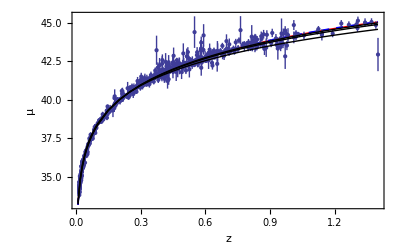

fig6a.eps

```mathematica
plot=Show[{plmon0,pllcdm,pldat,plmon1,plmon2,plmon3},Frame->True,PlotRange->All,FrameLabel->{"z","μ"},BaseStyle->mystyle,ImageSize->400]
Export["fig6a.eps",plot]
```

```mathematica
(* Figure 6a residuals *)
```

```mathematica
plresdat=ErrorListPlot[({{datanw[[#,2]],datanw[[#,3]]-(5 Log[10,dlzlcdm[datanw[[#,2]]]]+mb/.chminlcdm[[2]])},ErrorBar[datanw[[#,4]]]}&/@Range[ndat]),Frame->True,PlotRange->All,FrameLabel->{"z","μ - μ_ΛCDM"},BaseStyle->mystyle];
```

```mathematica
plmon0res=Plot[(5 Log[10,dlzmon0[z]]+mb/.chminmon[[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]]),{z,0.01,1.4},PlotStyle->{Red}];
```

```mathematica
rr=0.25;
list1=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]])},{z,0.01,0.09,0.01}];
list2=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]])},{z,0.10,1.4,0.05}];
list=ArrayFlatten[{{list1},{list2}}]
plmon1res=ListPlot[list,Frame->True,Axes->False,Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->500,PlotStyle->{Thin,Black}];
```

{{0.01,0.0379325},{0.02,0.0358972},{0.03,0.0338753},{0.04,0.0318675},{0.05,0.0298754},{0.06,0.0279005},{0.07,0.0259437},{0.08,0.0240067},{0.09,0.0220904},{0.1,0.0201959},{0.15,0.0110837},{0.2,0.00263001},{0.25,-0.00512841},{0.3,-0.0121965},{0.35,-0.0186057},{0.4,-0.0244017},{0.45,-0.0296363},{0.5,-0.0343623},{0.55,-0.0386305},{0.6,-0.0424876},{0.65,-0.0459762},{0.7,-0.0491342},{0.75,-0.0519959},{0.8,-0.0545919},{0.85,-0.0569493},{0.9,-0.059092},{0.95,-0.0610415},{1.,-0.0628168},{1.05,-0.0644347},{1.1,-0.0659103},{1.15,-0.0672571},{1.2,-0.068487},{1.25,-0.0696107},{1.3,-0.0706379},{1.35,-0.071577},{1.4,-0.072436}}

```mathematica
rr=0.5;
list1=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]])},{z,0.01,0.09,0.01}];
list2=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]])},{z,0.10,1.4,0.05}];
list=ArrayFlatten[{{list1},{list2}}]
plmon2res=ListPlot[list,Frame->True,Axes->False,Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->500,PlotStyle->{Thin,Black}];
```

{{0.01,0.0837763},{0.02,0.0795386},{0.03,0.0753246},{0.04,0.0711329},{0.05,0.0669646},{0.06,0.0628193},{0.07,0.0586985},{0.08,0.0546032},{0.09,0.0505348},{0.1,0.0464954},{0.15,0.0267968},{0.2,0.00810429},{0.25,-0.00939449},{0.3,-0.0255988},{0.35,-0.0404883},{0.4,-0.0541024},{0.45,-0.0665154},{0.5,-0.0778197},{0.55,-0.0881133},{0.6,-0.0974924},{0.65,-0.106048},{0.7,-0.113863},{0.75,-0.121014},{0.8,-0.127569},{0.85,-0.133589},{0.9,-0.139127},{0.95,-0.144231},{1.,-0.148944},{1.05,-0.153303},{1.1,-0.157342},{1.15,-0.16109},{1.2,-0.164573},{1.25,-0.167816},{1.3,-0.170839},{1.35,-0.173661},{1.4,-0.176299}}

```mathematica
rr=5;
list1=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]])},{z,0.01,0.09,0.01}];
list2=Table[{z,(5 Log[10,dlzmon[z,rr]]+mb/.chminmonr[rr][[2]])-(5 Log[10,dlzlcdm[z]]+mb/.chminlcdm[[2]])},{z,0.10,1.4,0.05}];
list=ArrayFlatten[{{list1},{list2}}]
plmon3res=ListPlot[list,Frame->True,Axes->False,Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->500,PlotStyle->{Thin,Black}];
```

{{0.01,0.208719},{0.02,0.197491},{0.03,0.186431},{0.04,0.175535},{0.05,0.164803},{0.06,0.154229},{0.07,0.143813},{0.08,0.133551},{0.09,0.12344},{0.1,0.113478},{0.15,0.0658192},{0.2,0.0215242},{0.25,-0.019683},{0.3,-0.0580541},{0.35,-0.0938177},{0.4,-0.127182},{0.45,-0.158337},{0.5,-0.187454},{0.55,-0.214693},{0.6,-0.240197},{0.65,-0.264101},{0.7,-0.286526},{0.75,-0.307585},{0.8,-0.327381},{0.85,-0.346009},{0.9,-0.363556},{0.95,-0.380101},{1.,-0.395718},{1.05,-0.410472},{1.1,-0.424427},{1.15,-0.437639},{1.2,-0.450159},{1.25,-0.462035},{1.3,-0.473311},{1.35,-0.484027},{1.4,-0.494221}}

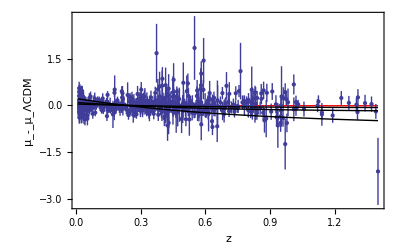

fig6a_residuals.eps

```mathematica
plot=Show[{plmon0res,plresdat,plmon1res,plmon2res,plmon3res},Frame->True,PlotRange->All,FrameLabel->{"z","μ_-_μ_ΛCDM"},BaseStyle->mystyle,ImageSize->400,PlotRangePadding->{{0.01,Automatic},Automatic}]
Export["fig6a_residuals.eps",plot]
```

```mathematica
(* Figure 6b *)
```

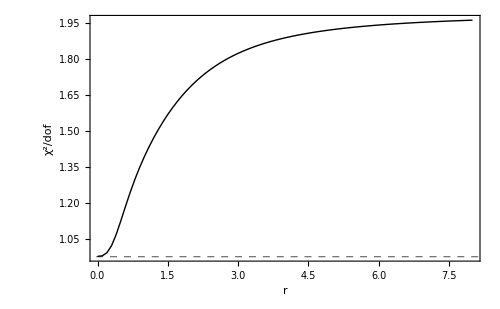

fig6b.eps

```mathematica
Off[InterpolatingFunction::dmval];
chi2monr[mb_,r_]:=Sum[(mgndat[i]-5 Log[10,dlzmon[zdat[i],r]]-mb)^2/(errdat[i]^2+(sint)^2),{i,1,ndat}];
chminmonr[r_]:=FindMinimum[chi2monr[mb,r],{mb,0}];
rr=.;
rr[n_]=8/80(n-1);
Do[dot[n]=chminmonr[rr[n]]/ndat,{n,1,81}]
points=Table[{rr[n],dot[n][[1]]},{n,1,81}];
plot=ListPlot[points,Frame->True,Axes->False,FrameLabel->{"r","χ^2/dof"},Joined->True,PlotRange->All,BaseStyle->mystyle,ImageSize->400,GridLines->{{},{chminlcdm[[1]]/ndat}},GridLinesStyle->Directive[Black,Thin,Dashed],PlotStyle->Black]
Export["fig6b.eps",plot]
```